```mathematica
SetDirectory[NotebookDirectory[]];
countryWideConfirmed=Import["./COVID-19/csse_covid_19_data/csse_covid_19_time_series/time_series_covid19_confirmed_global.csv","CSV"];
```

```mathematica
countryWideConfirmedExChina = DeleteCases[countryWideConfirmed,{_,"China",__}];
countryWideConfirmedExChina=Drop[countryWideConfirmedExChina,1,{1,4}];
globalConfirmedExChina = Transpose[{Total[countryWideConfirmedExChina,{1}]}];
dataGlobal=MapThread[Prepend,{globalConfirmedExChina,Table[a,{a,0,Length[globalConfirmedExChina]-1,1}]}]

confirmedUS = Cases[countryWideConfirmed,{_,"US",__}];
confirmedUS=Transpose[Drop[confirmedUS,0,{1,4}]];
dataUS=MapThread[Prepend,{confirmedUS,Table[a,{a,0,Length[confirmedUS]-1,1}]}]
```

{{0,7},{1,11},{2,21},{3,28},{4,43},{5,50},{6,69},{7,79},{8,93},{9,125},{10,147},{11,157},{12,165},{13,185},{14,195},{15,207},{16,281},{17,306},{18,321},{19,408},{20,416},{21,462},{22,473},{23,527},{24,617},{25,711},{26,824},{27,925},{28,1020},{29,1120},{30,1269},{31,1571},{32,1936},{33,2320},{34,2652},{35,3222},{36,4146},{37,5184},{38,6655},{39,8437},{40,10170},{41,12579},{42,14734},{43,17349},{44,21111},{45,25077},{46,28998},{47,32730},{48,37733},{49,44954},{50,47420},{51,64260},{52,75124},{53,86451},{54,100541},{55,116044},{56,133719},{57,161414},{58,190958},{59,223202},{60,255518},{61,296737},{62,336454},{63,385992},{64,447809},{65,511394},{66,578694},{67,638018},{68,700191},{69,775208},{70,850244},{71,931034},{72,1013406},{73,1114865},{74,1189513},{75,1262436},{76,1343378},{77,1428295},{78,1512467},{79,1608778},{80,1688500}}

{{0,1},{1,1},{2,2},{3,2},{4,5},{5,5},{6,5},{7,5},{8,5},{9,7},{10,8},{11,8},{12,11},{13,11},{14,11},{15,11},{16,11},{17,11},{18,11},{19,11},{20,12},{21,12},{22,13},{23,13},{24,13},{25,13},{26,13},{27,13},{28,13},{29,13},{30,15},{31,15},{32,15},{33,51},{34,51},{35,57},{36,58},{37,60},{38,68},{39,74},{40,98},{41,118},{42,149},{43,217},{44,262},{45,402},{46,518},{47,583},{48,959},{49,1281},{50,1663},{51,2179},{52,2727},{53,3499},{54,4632},{55,6421},{56,7783},{57,13747},{58,19273},{59,25600},{60,33276},{61,43847},{62,53740},{63,65778},{64,83836},{65,101657},{66,121465},{67,140909},{68,161831},{69,188172},{70,213372},{71,243762},{72,275586},{73,308853},{74,337072},{75,366667},{76,396223},{77,429052},{78,461437},{79,496535},{80,526396}}

```mathematica
lessFancyModel[r_?NumberQ,k_?NumberQ,p_?NumberQ,c0_?NumberQ]:=Module[{c,t},First[c/.NDSolve[{c'[t]==r*c[t]^p*(1-(c[t]/k)),c[0]==c0},c,{t,0,110}]]]
fancyFitUS=NonlinearModelFit[dataUS,{lessFancyModel[r,k,p,c0][t]},{{r,.2},k,p,c0},t]
fancyFitUS["ParameterConfidenceIntervalTable"]
fancyFitUS["RSquared"]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[InterpolatingFunction[{{0., 110.}}, <>][t]]

| Estimate | Standard Error | Confidence Interval
r | 0.360529 | 0.0996219 | {0.162156,0.558901}
k | 689024. | 19174.2 | {650843.,727205.}
p | 0.950499 | 0.0239312 | {0.902846,0.998152}
c0 | 0.0000597173 | 0.000475112 | {-0.000886352,0.00100579}

0.999591

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

| Estimate | Standard Error | Confidence Interval
a | 150.721 | 0.00126465 | {150.718,150.723}
b | 0.204137 | 0.00301537 | {0.198132,0.210141}
c | 656134. | 9966.65 | {636288.,675981.}
d | 10.0165 | 0.190608 | {9.63696,10.3961}

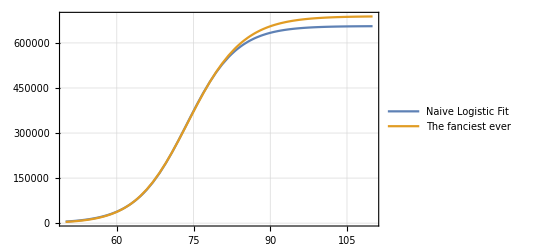

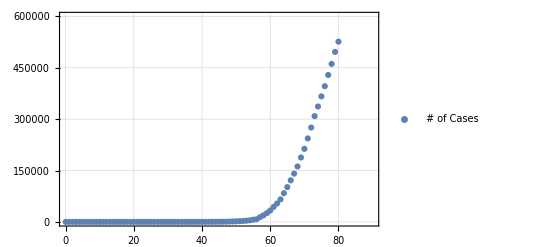

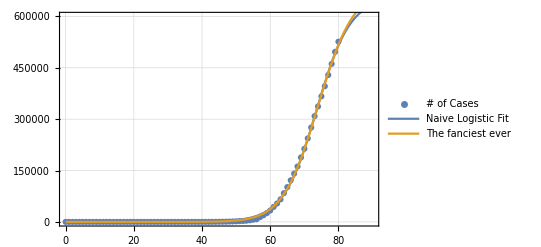

```mathematica
fitLogUS=NonlinearModelFit[dataUS,c/(1+a*Exp[-b t+d]),{a,b,c,d},t];
fitLogUS["ParameterConfidenceIntervalTable"]
Plot[{Normal[fitLogUS],Normal[fancyFitUS]},{t,50,110},PlotRange->All,PlotLegends->{"Naive Logistic Fit","The fanciest ever"},Frame->True,GridLines->Automatic]
scatterPlotUS=ListPlot[dataUS,PlotRange->{{0,90},{0,600000}},Frame->True,GridLines->Automatic,PlotLegends->{"# of Cases"}]
fitPlotsUS=Plot[{Normal[fitLogUS],Normal[fancyFitUS]},{t,0,100},PlotRange->All,PlotLegends->{"Naive Logistic Fit","The fanciest ever"}];
Show[scatterPlotUS,fitPlotsUS]
```

```mathematica
fancyModel[r_?NumberQ,k_?NumberQ,p_?NumberQ,c0_?NumberQ]:=Module[{c,t},First[c/.NDSolve[{c'[t]==r*c[t]^p*(1-(c[t]/k)),c[0]==c0},c,{t,0,110}]]]
fancyFitGlobal=NonlinearModelFit[dataGlobal,{fancyModel[r,k,p,c0][t]},{{r,.2},k,p,c0},t]
fancyFitGlobal["ParameterConfidenceIntervalTable"]
fancyFitGlobal["RSquared"]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[InterpolatingFunction[{{0., 110.}}, <>][t]]

| Estimate | Standard Error | Confidence Interval
r | 0.433617 | 0.065358 | {0.303473,0.563762}
k | 2.46104×10^6 | 45983.9 | {2.36947×10^6,2.5526×10^6}
p | 0.918904 | 0.0119318 | {0.895145,0.942663}
c0 | 0.00620107 | 0.0199749 | {-0.033574,0.0459761}

0.999905

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

(2.23285×10^6)/(1+65.8093 ⅇ^(7.16956-0.155341 t))

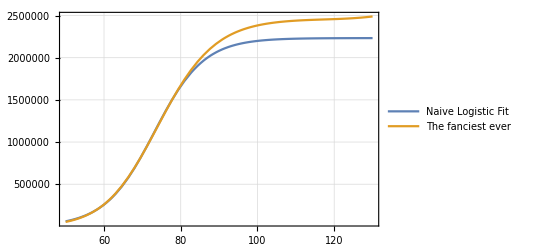

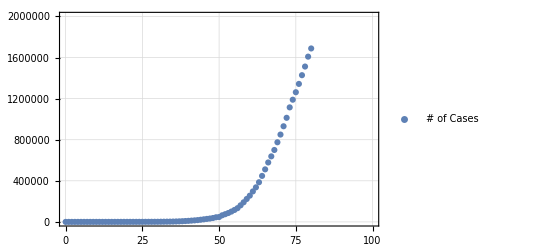

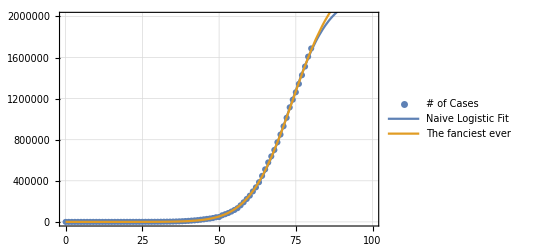

```mathematica
fitLogGlobal=NonlinearModelFit[dataGlobal,c/(1+a*Exp[-b t+d]),{a,b,c,d},t];
Normal[fitLogGlobal]
Plot[{Normal[fitLogGlobal],Normal[fancyFitGlobal]},{t,50,130},PlotRange->All,PlotLegends->{"Naive Logistic Fit","The fanciest ever"},Frame->True,GridLines->Automatic]
scatterPlotGlobal=ListPlot[dataGlobal,PlotRange->{{0,100},{0,2000000}},Frame->True,GridLines->Automatic,PlotLegends->{"# of Cases"}]
fitPlotsGlobal=Plot[{Normal[fitLogGlobal],Normal[fancyFitGlobal]},{t,0,100},PlotRange->All,PlotLegends->{"Naive Logistic Fit","The fanciest ever"}];
Show[scatterPlotGlobal,fitPlotsGlobal]
```